```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/final_para/phase

# Data

## Tc220 alpha0.5

```mathematica
mf=Table[Transpose[Import["./Tc220a0p5/TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,37}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,37}];
mub=Flatten[{Table[i*15,{i,1,37}]}];
Tpc=Table[FindMaximum[{intdmfdt[[i]],80<x<190},{x,150}][[2]][[1]][[2]],{i,1,37}];
peak=Table[FindMaximum[{intdmfdt[[i]],80<x<190},{x,150}][[1]],{i,1,37}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+2}][[1]][[2]],{i,1,37}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-5}][[1]][[2]],{i,1,37}];
fitTpc=FindFit[Transpose[{mub,Tpc}],a+b x^2+c x^4(*+d x^6*),{a,b,c},x];
fitTpcup=FindFit[Transpose[{mub,Tpcup80}],a+b x^2+c x^4,{a,b,c},x];
fitTpcdown=FindFit[Transpose[{mub,Tpcdown80}],a+b x^2+c x^4,{a,b,c},x];
pbT220a0p5=Transpose[{mub,Tpc}];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

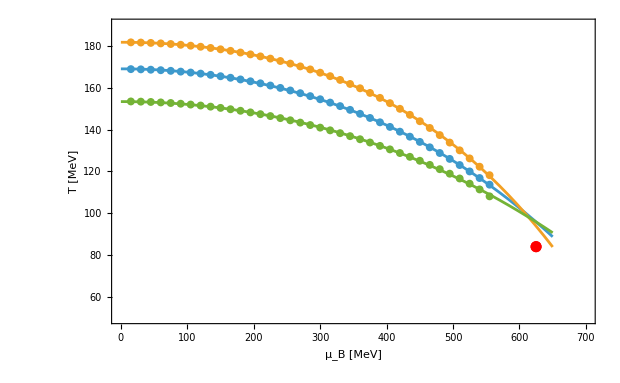

```mathematica
Show[ListPlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]},PlotRange->{{0,700},{50,190}}],Plot[{a+b x^2+c x^4/.fitTpc,a+b x^2+c x^4/.fitTpcup,a+b x^2+c x^4/.fitTpcdown},{x,0,650}],ListPlot[{{625,84}},PlotStyle->Red],Frame->True,FrameLabel->{Style["μ_B [MeV]",15,Black],Style["T [MeV]",15,Black]}]
```

## Tc225 alpha0.5

```mathematica
mf=Table[Transpose[Import["./Tc225a0p5/TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,37}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,37}];
mub=Flatten[{Table[i*15,{i,1,37}]}];
Tpc=Table[FindMaximum[{intdmfdt[[i]],80<x<190},{x,150}][[2]][[1]][[2]],{i,1,37}];
peak=Table[FindMaximum[{intdmfdt[[i]],80<x<190},{x,150}][[1]],{i,1,37}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+2}][[1]][[2]],{i,1,37}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-5}][[1]][[2]],{i,1,37}];
fitTpc=FindFit[Transpose[{mub,Tpc}],a+b x^2+c x^4(*+d x^6*),{a,b,c},x];
fitTpcup=FindFit[Transpose[{mub,Tpcup80}],a+b x^2+c x^4,{a,b,c},x];
fitTpcdown=FindFit[Transpose[{mub,Tpcdown80}],a+b x^2+c x^4,{a,b,c},x];
pbT225a0p5=Transpose[{mub,Tpc}];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

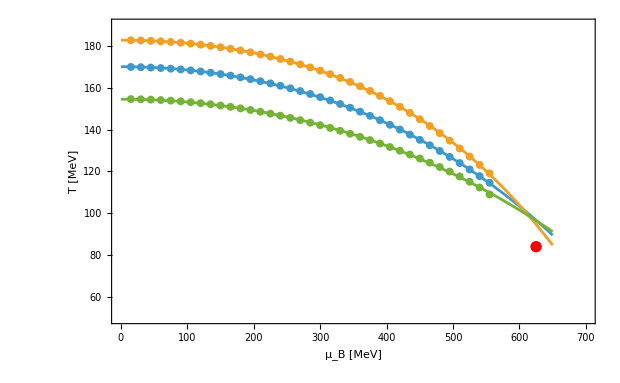

```mathematica
Show[ListPlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]},PlotRange->{{0,700},{50,190}}],Plot[{a+b x^2+c x^4/.fitTpc,a+b x^2+c x^4/.fitTpcup,a+b x^2+c x^4/.fitTpcdown},{x,0,650}],ListPlot[{{625,84}},PlotStyle->Red],Frame->True,FrameLabel->{Style["μ_B [MeV]",15,Black],Style["T [MeV]",15,Black]}]
```

## Compare plot

```mathematica
mubfo[sqrts_]:=1307.5/(1+0.288 sqrts);
sqrts[muB_]:=-(1.7361111111111112 (-2615.+2. muB))/muB;
Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/muB-1)/0.288]/0.45]);
STARFitI=Transpose[{Flatten[Import["./Tc220a0p5/freezeout/mub.dat"]],Flatten[Import["./Tc220a0p5/freezeout/STARFitI.dat"]]}];
STARFitII=Transpose[{Flatten[Import["./Tc220a0p5/freezeout/mub.dat"]],Flatten[Import["./Tc220a0p5/freezeout/STARFitII.dat"]]}];
TI=Table[Interpolation[STARFitI][mub[[i]]],{i,2,Length[mub]}];
TII=Table[Interpolation[STARFitII][mub[[i]]],{i,2,Length[mub]}];
```

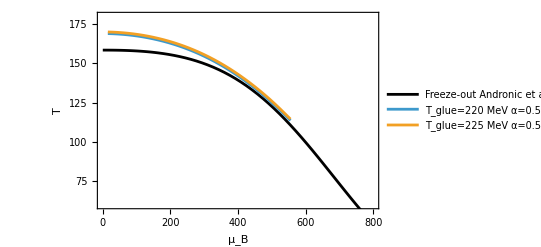

./phase.pdf

```mathematica
Freezeoutplot=Plot[Tfo[x],{x,0,800},PlotStyle->Black,PlotLegends->Placed[{"Freeze-out Andronic et al."},{Right,Top}]];
Phase=ListLinePlot[{pbT220a0p5,pbT225a0p5},PlotLegends->Placed[{"T_glue=220 MeV α=0.5","T_glue=225 MeV α=0.50","T_glue=240 MeV α=0.40","T_glue=240 MeV α=0.50"},{Left,Bottom}]];
Show[Freezeoutplot,Phase,PlotRange->{All,{60,180}},Frame->True,FrameLabel->{Style["μ_B",15,Black],Style["T",15,Black]}]
Export["./phase.pdf",%]
```